### Settings

```mathematica
dx = 4.58/0.529;
dy = 6.48/0.529;
a=132.7/0.529;
delta =0.0001;
rMax=200; 
Z =0.04; 
m = 0.152;
coord = {{0,-3.5*dy},{0,3.5*dy},{-4*dx, 1.5*dy},{4*dx, 1.5*dy}, {-4*dx, -1.5dy},{4*dx, -1.5dy}};
```

Options::optnf: FormatType is not a known option for {OutputStream[/Users/danis/Science/Software/Mathematica_scripts/data_1.dat,3]}.

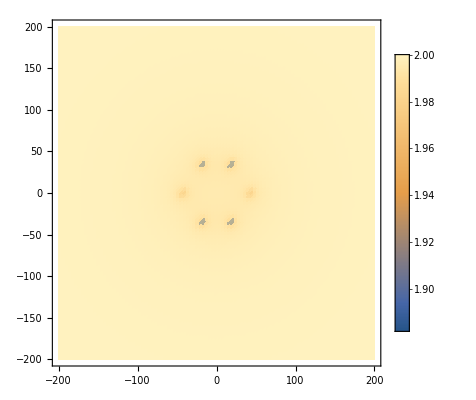

```mathematica
V[r_, θ_] := Sum[(-Z)/(Sqrt[(r*Sin[θ]- coord[[i]][[1]])^2  + (r*Cos[θ]-coord[[i]][[2]])^2]+delta)*Exp[-Sqrt[(r*Sin[θ]-coord[[i]][[1]])^2  + (r*Cos[θ]-coord[[i]][[2]])^2]/a],{i,6} ] +2;
DensityPlot[V[r ,θ]/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y],{x,-rMax,rMax},{y,-rMax,rMax}, (*PlotTheme->"Minimal",*) PlotPoints->100,  PlotLegends->Automatic, PlotRange->All]
Export[NotebookDirectory[]<>"Coulomb.png",%,ImageResolution->100];
```

### 2 D Problem

```mathematica
{egnVal,egnVec}=NDEigensystem[
{(-1/(2*m))* Laplacian[R2D[r,θ],{r,θ},"Polar"]+V[r,θ]*R2D[r,θ],
DirichletCondition[R2D[r,θ]==0,r==rMax*Sqrt[2]&&0<θ<=2*Pi],
PeriodicBoundaryCondition[R2D[r,θ],θ==0,TranslationTransform[{0,2 π}]]},
R2D[r,θ],{r,0,rMax*Sqrt[2]},{θ,0,2 π},8, Method->{"Eigensystem"->{"Arnoldi","MaxIterations"->1000000}(* "Direct"*),"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}}}  ];
ord =Ordering[egnVal];
Sort[Re[egnVal]]
```

Options::optnf: FormatType is not a known option for {OutputStream[/Users/danis/Science/Software/Mathematica_scripts/data_1.dat,3]}.

{1.99572,1.99831,1.99841,1.99965,2.00009,2.0001,2.00022,2.00026}

Options::optnf: FormatType is not a known option for {OutputStream[/Users/danis/Science/Software/Mathematica_scripts/data_1.dat,3]}.

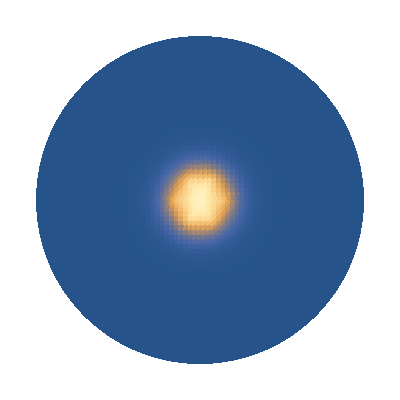

```mathematica
F1 =Part[Re[egnVec],Part[ord,1]]^2;
DensityPlot[F1/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y],{x,-2rMax,2rMax},{y,-2rMax,2rMax}, PlotTheme->"Minimal",  PlotPoints->100, PlotRange->All];
DensityPlot[F1/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y]+2π,{x,-2rMax,2rMax},{y,-2rMax,2rMax}, PlotTheme->"Minimal", PlotPoints->100,PlotRange->All  (*PlotLegends->Automatic*)];
Show[{%,%%}]
Export[NotebookDirectory[]<>"1.png",%,ImageResolution->100];
```

Options::optnf: FormatType is not a known option for {OutputStream[/Users/danis/Science/Software/Mathematica_scripts/data_1.dat,3]}.

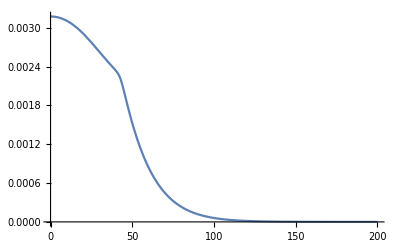

```mathematica
Plot[F1/.r->x/.θ->0, {x, 0, rMax},PlotRange->All]
Export[NotebookDirectory[]<>"1_line.png",%,ImageResolution->100];
```

```mathematica
str=OpenWrite[NotebookDirectory[]<>"data_2.dat", FormatType->StandardForm];
$Output={str};
Do[Print[x ,"  ",  F1/.r->x/.θ->0], {x, 0, rMax, 0.1 }];
Close[str];
```